The purpose of this notebook is to demonstrate the conflict between measured optical constants for Iron and the theoretical prediction modelling the conduction electrons as a plasma in a homogeneous background.

### Extract Iron Data

This data is taken from a book of optical measurments by Palik (https://doi.org/10.1016/B978-012544415-6.50000-5 )

Data was extracted from Screenshots of tables in the book using  https://www.docsumo.com/free-tools/extract-tables-from-pdf-images

#### Import Data

```mathematica
opticaliron1 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_1.csv"][[2;;,;;3]];
opticaliron2 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_2.csv"][[2;;,;;3]];
opticaliron3 = ToExpression[Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_3.csv"][[2;;,;;3]]];
```

#### Assign to variables

```mathematica
kFe= Join[opticaliron1[[;;,3]],opticaliron2[[;;,3]],opticaliron3[[;;,3]]]; (*[]*)
nFe= Join[opticaliron1[[;;,2]],opticaliron2[[;;,2]],opticaliron3[[;;,2]]]; (*[]*)
ωFe= Join[opticaliron1[[;;,1]],opticaliron2[[;;,1]],opticaliron3[[;;,1]]]; (*[eV]*)
```

#### Convert to ϵ

The following relation between k, n and ϵ where given in Palik

```mathematica
ϵFe = ComplexExpand[nFe^2- kFe^2 + 2 I nFe kFe] ;
ELFFe = Im[-1/ϵFe];
```

#### Plot the results

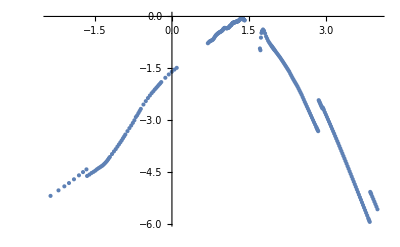

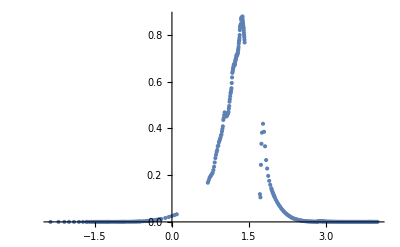

```mathematica
ELFFeData = Table[{ωFe[[i]],ELFFe[[i]]},{i,Length[ωFe]}];
logELFFeData =Table[{Log[10,ωFe[[i]]],ELFFe[[i]]},{i,Length[ωFe]}];
loglogELFFeData =Table[{Log[10,ωFe[[i]]],Log10[ELFFe[[i]]]},{i,Length[ωFe]}];
ListPlot[%,PlotRange->All]
ListPlot[%%%,PlotRange->All]
```

### Get Theory Prediction

#### Optical Mermin Function

We now consider the optical limit of the Mermin dielectric

```mathematica
(*ϵM[ω/(2 qF vF z),z,ν/(2 qF vF z)];
Limit[%,z->0]*)
```

The constants in the above can be written simply as the square of the Plasmon Frequency

```mathematica
4/3(qF vF χ)^2==4/3(ℏ/m(3 π^2 ne)^(2/3)√((m e^2)/(π ℏ^2(3 π^2 ne)^(1/3))1/(4 π ϵ0)))^2==ωp^2
```

4/3 qF^2 vF^2 χ^2==(e^2 ne)/(m ϵ0)==ωp^2

So our optical Mermin Dielectric is given by the simple expression below.

```mathematica
ϵMq0[ω,ν,ωp]
```

1-ωp^2/(ω (ⅈ ν+ω))

This is precisely the Drude Dielectric:

https://www.researchgate.net/publication/312007841_Dielectric_function_for_free_electron_gas_Comparison_between_Drude_and_Lindhard_models

#### Optical Loss Function

Using the Drude / Optical Mermin dielectric, we get the following loss function:

```mathematica
Information[ELFM0]
```

```mathematica
ELFM0[ω,ν,ωp]
```

(ν ω ωp^2)/(ν^2 ω^2+(ω^2-ωp^2)^2)

### Compare Data and Theory

#### Plot the two

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" ν[]/.SIcoreparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Orange,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"8 e^-"],Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" ν[]/.SIcoreparamsp5),"ℏ" "ωp"/.SIcrustparamsp5]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Green,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"1/2 e^-"],ListPlot[loglogELFFeData,PlotRange->All]
}]
```

-Graphics-

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" ν[]/.SIcrustparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Orange,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"8 e^-"],Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" ν[]/.SIParams[290,neSIIron[7800,0.03]]),"ℏ" "ωp"/.SIParams[290,neSIIron[7800,0.03]]]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Green,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"0.03 e^-"],ListPlot[loglogELFFeData,PlotRange->All]
}]
```

-Graphics-

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" ν[]/.SIcrustparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Orange,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"8 e^-"],ListPlot[loglogELFFeData,PlotRange->All]
}]
```

-Graphics-

#### Fit Drude Dielectric to the Tail

Here, we assume that we have correctly characterized the conduction electron number density (and hence the Plasmon Frequency).  As such we look to find the value of the collision frequency such that the theory prediction matches the low energy tail of the data (where we expect our model to be valid)

Isolate the low energy tail of the Loss Function Data

```mathematica
DataTail = SortBy[loglogELFFeData,First][[;;8]];
```

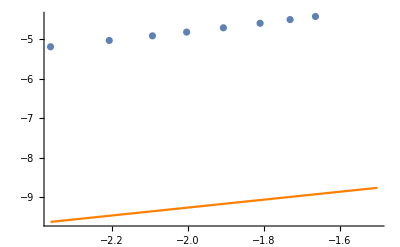

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" ν[]/.SIcrustparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],-1.5},PlotStyle->Orange,PlotRange->All],ListPlot[DataTail,PlotRange->All,AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_Fe](ω)"]
}]
```

Now we fit - Assuming the conduction electron number density is correct.

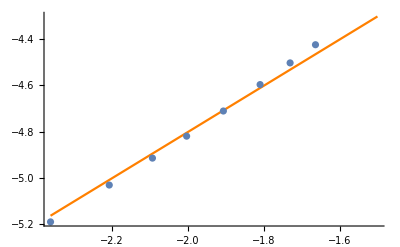

{νrescale→28861.2}

| Estimate | Standard Error | t-Statistic | P-Value
νrescale | 28861.2 | 600.917 | 48.0286 | 4.43796×10^-10

| DF | SS | MS
Model | 1 | 182.775 | 182.775
Error | 7 | 0.00457886 | 0.000654123
Uncorrected Total | 8 | 182.779 | 
Corrected Total | 7 | 0.493581 |

χ^2 / ndof is given by: error / MS

```mathematica
FeFit=NonlinearModelFit[DataTail,Log10[ELFM0[10^ω "JpereV" /.SIConstRepl,νrescale ("ℏ" ν[]/.SIcrustparams) ,"ℏ""ωp"/.SIcrustparams]],{νrescale},ω];
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,(νrescale /.FeFit["BestFitParameters"])("ℏ" ν[]/.SIcrustparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],-1.5},PlotStyle->Orange,PlotRange->All],ListPlot[DataTail,PlotRange->All,AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_Fe](ω)"]
}]
FeFit["BestFitParameters"]
FeFit["ParameterTable"]
FeFit["ANOVATable"]
Print["χ^2 / ndof is given by: error / MS"]
```

#### Expansion at the tail

It is also worth noting, that at the low energy tail:

```mathematica
{"ℏ""ωp","ℏ"ν[]}/.SIcrustparams
"JpereV" /.SIConstRepl (*>~ω at the tail*)
```

{4.8854×10^-18,8.15857×10^-24}

1.602×10^-19

So we can expand in large ωp

```mathematica
Series[ELFM0[ω,ν, ωp],{ωp,∞,3}]
```

(ν ω)/ωp^2+O[1/ωp]^4

So it could be that the number density (ωp α ne) is off by the reciprocal factor. Ie. too large by a factor of νrescale, but this seems unlikely since the samples are O(100) atoms thick, and so should represent bulk Iron well.

#### Conclusions - *** see the new one

It seems that the collision frequency we found for a two component plasma is too small by a factor of

```mathematica
νrescale/.FeFit["BestFitParameters"]
```

28861.2

Hence: it seems likely that there is an issue with the collision rate. Perhaps some of the following are the issue
	- we have applied it incorrectly, and it is not appropriate for use with solid Iron conduction electrons
	- there is a mistake somewhere in the code or unit conversion

#### New n_eff Conclusion

The discrepancy at the tail is alleviated when we take the number of conduction electrons in Iron to be 0.5. However we need around 8 to match on to the location of the plasmon resonance. 

So we have good agreement with the data so long as we can have an ω dependent number of effective electrons. 

From the plot below found in Pines, it seems that there is precedent for this. Copper is also a transition metal like Iron and has almost exactly this behaviour.

-Graphics-